FittedModel[13.6013-0.0794677 x]

{{12.41,14.7927},{-0.101047,-0.0578881}}

| Estimate | Standard Error | t-Statistic | P-Value
1 | 13.6013 | 0.575896 | 23.6177 | 1.2532×10^-17
x | -0.0794677 | 0.0104317 | -7.61792 | 9.82817×10^-8

{13.6013-0.0794677 x-2.06866 √(0.331656-0.0114296 x+0.00010882 x^2),13.6013-0.0794677 x+2.06866 √(0.331656-0.0114296 x+0.00010882 x^2)}

{13.6013-0.0794677 x-2.06866 √(1.12011-0.0114296 x+0.00010882 x^2),13.6013-0.0794677 x+2.06866 √(1.12011-0.0114296 x+0.00010882 x^2)}

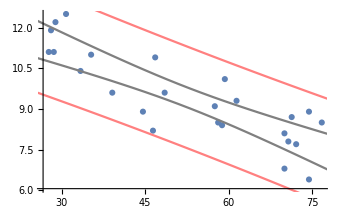

0.716164

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 45.756 | 45.756 | 58.0328 | 9.82817×10^-8
Error | 23 | 18.1344 | 0.788452 |  | 
Total | 24 | 63.8904 |  |  |

```mathematica
data={{35.3,11.0},{27.7,11.1},{30.8,12.5},{58.8,8.4},{61.4,9.3},{71.3,8.7},{74.4,6.4},{76.7,8.5},{70.7,7.8},{57.5,9.1},{46.4,8.2},{28.9,12.2},{28.1,11.9},{39.1,9.6},{46.8,10.9},{48.5,9.6},{59.3,10.1},{70,8.1},{70,6.8},{74.4,8.9},{72.1,7.7},{58.1,8.5},{44.6,8.9},{33.4,10.4},{28.6,11.1}};
model=LinearModelFit[data,x,x]
model["ParameterConfidenceIntervals",ConfidenceLevel->0.95]
model["ParameterTable"]
conf=model["MeanPredictionBands",ConfidenceLevel->0.95]
pred=model["SinglePredictionBands",ConfidenceLevel->0.95]
Show[ListPlot[data],Plot[conf,{x,0,100},PlotStyle->Gray],Plot[pred,{x,0,100},PlotStyle->Pink]]
model["RSquared"]
model["ANOVATable"]
```

```mathematica
InverseCDF[FRatioDistribution[3,10],0.95]
```

3.70826